```mathematica
ClearAll["Global`*"]
```

```mathematica
vv:=2
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K2[n_] := If[Floor[n^(1/2)]==n^(1/2),K[n^(1/2)],0]
K6[n_] := K[n]-If[ Floor[Log[vv,n]]==Log[vv,n],n /Log[vv,n],0]
P[n_,0]=1; 
P[n_, k_] := P[n,k] = Sum[ K2[j]P[Floor[n/j],k-1],{j,2,n}]
En[n_] := En[n] = Sum[ 1/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,z_] := En[n] = Sum[ (z^k)/(k!) P[n,k],{k,0, Log[2,n]}]
en[n_] := En[n]-En[n-1]
LAdd[n_] := Sum[ vv^k/k,{k,1,Log[vv,n]}]
LAdd2[n_] := Sum[(-1)^k vv^k,{k,1,Log[vv,n]}]
PP[n_,k_] := PP[n,k]=Sum[ 1/k-PP[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
P[10000,1]
```

428/15

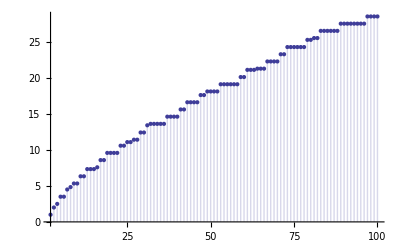

```mathematica
DiscretePlot[{P[n^2,1]},{n,2,100}]
```

```mathematica
Table[{n,en[n]},{n,2,50}]//TableForm
```

2 | 0
3 | 0
4 | 1
5 | 0
6 | 0
7 | 0
8 | 0
9 | 1
10 | 0
11 | 0
12 | 0
13 | 0
14 | 0
15 | 0
16 | 1
17 | 0
18 | 0
19 | 0
20 | 0
21 | 0
22 | 0
23 | 0
24 | 0
25 | 1
26 | 0
27 | 0
28 | 0
29 | 0
30 | 0
31 | 0
32 | 0
33 | 0
34 | 0
35 | 0
36 | 1
37 | 0
38 | 0
39 | 0
40 | 0
41 | 0
42 | 0
43 | 0
44 | 0
45 | 0
46 | 0
47 | 0
48 | 0
49 | 1
50 | 0

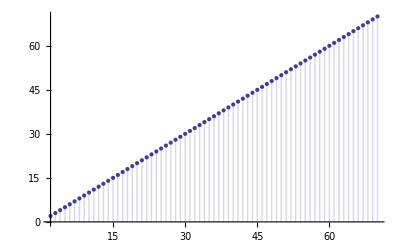

```mathematica
DiscretePlot[En[n^2],{n,2,70}]
```

```mathematica
Table[ {n, En[n], Floor[n^(1/2)]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 1 | 1
3 | 1 | 1
4 | 2 | 2
5 | 2 | 2
6 | 2 | 2
7 | 2 | 2
8 | 2 | 2
9 | 3 | 3
10 | 3 | 3
11 | 3 | 3
12 | 3 | 3
13 | 3 | 3
14 | 3 | 3
15 | 3 | 3
16 | 4 | 4
17 | 4 | 4
18 | 4 | 4
19 | 4 | 4
20 | 4 | 4
21 | 4 | 4
22 | 4 | 4
23 | 4 | 4
24 | 4 | 4
25 | 5 | 5
26 | 5 | 5
27 | 5 | 5
28 | 5 | 5
29 | 5 | 5
30 | 5 | 5
31 | 5 | 5
32 | 5 | 5
33 | 5 | 5
34 | 5 | 5
35 | 5 | 5
36 | 6 | 6
37 | 6 | 6
38 | 6 | 6
39 | 6 | 6
40 | 6 | 6
41 | 6 | 6
42 | 6 | 6
43 | 6 | 6
44 | 6 | 6
45 | 6 | 6
46 | 6 | 6
47 | 6 | 6
48 | 6 | 6
49 | 7 | 7
50 | 7 | 7
51 | 7 | 7
52 | 7 | 7
53 | 7 | 7
54 | 7 | 7
55 | 7 | 7
56 | 7 | 7
57 | 7 | 7
58 | 7 | 7
59 | 7 | 7
60 | 7 | 7
61 | 7 | 7
62 | 7 | 7
63 | 7 | 7
64 | 8 | 8
65 | 8 | 8
66 | 8 | 8
67 | 8 | 8
68 | 8 | 8
69 | 8 | 8
70 | 8 | 8
71 | 8 | 8
72 | 8 | 8
73 | 8 | 8
74 | 8 | 8
75 | 8 | 8
76 | 8 | 8
77 | 8 | 8
78 | 8 | 8
79 | 8 | 8
80 | 8 | 8
81 | 9 | 9
82 | 9 | 9
83 | 9 | 9
84 | 9 | 9
85 | 9 | 9
86 | 9 | 9
87 | 9 | 9
88 | 9 | 9
89 | 9 | 9
90 | 9 | 9
91 | 9 | 9
92 | 9 | 9
93 | 9 | 9
94 | 9 | 9
95 | 9 | 9
96 | 9 | 9
97 | 9 | 9
98 | 9 | 9
99 | 9 | 9
100 | 10 | 10